### Optimal Response and Cost Calculation for an Eager Strategy

```mathematica
(*Step 1:Define constants*)
λ=20;
κ=0.1;
σ=10;

(*Step 2:Define b[t]*)
b[t_]:=(Exp[-σ t]-1)/(Exp[-σ]-1);

(*Step 3:Solve for function a[t]*)
aSol=NDSolve[{a''[t]==-(λ/2) (D[b[t],{t,2}]+κ D[b[t],t]),a[0]==0,a[1]==1},a,{t,0,1}];
aFunc[t_]=a[t]/. First[aSol];

(*Step 4:Calculate the functionals*)
functional1=(D[aFunc[t],t]+λ D[b[t],t]) D[aFunc[t],t];
functional2=κ (aFunc[t]+λ b[t]) D[aFunc[t],t];

(*Step 5:Calculate the numerical value of the sum*)
sumFunctional=NIntegrate[functional1+functional2,{t,0,1}];

(*Output the result*)
sumFunctional
```

-369.234

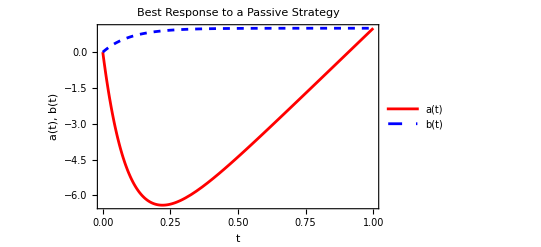

```mathematica
(*Plot both a(t) and b(t) with b(t) as a dashed line*)
Plot[
{aFunc[t],b[t]},{t,0,1},
PlotLegends->{"a(t)","b(t)"},
PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{
{"a(t), b(t)","σ="<>ToString[σ]},
{"t","κ="<>ToString[κ]<>", λ="<>ToString[λ]}},PlotLabel->"Best Response to a Passive Strategy",
PlotRange->All
]
```